```mathematica
(* ECUACIONES *)

(******************************************************************************)
(* FRECUENCIAS FASE NORMAL*)
(******************************************************************************)

Clear[ωzxn,ωzyn];
Clear[ω,ωo]
ω=1;
ωo=1;
(* ωzxn Frecuencia dependendiente z-x Fase Normal *)
ωzxn[ηz_,ηx_]:=ωo*√(1-(ηz-ηx)/ωo); 
(* ωzyn Frecuencia dependendiente z-y Fase Normal *)
ωzyn[ηz_,ηy_]:=1-(ηz-ηy)/ωo; 

(******************************************************************************)
(* FRECUENCIAS FASE SUPERRADIANTE *)
(******************************************************************************)

Clear[μx,ω1,ω2,ω3,ω4,ω5,ωzxs1,ωzxs2,ωzys1,ωzys2];
(* Resultado de eliminar términos lineales *)
μx[ηz_,ηx_,γ_,ξ_]:=1/((γ^2*(1+ξ)^2)/(ω*ωo)+(ηz-ηx)/ωo);

(* ω1 Frecuencia relacionada con d^*d *)
ω1[ηz_,ηx_,γ_,ξ_]:=1/2((ωo/μx[ηz,ηx,γ,ξ]-ηz)*(1+μx[ηz,ηx,γ,ξ])+ηx*(1-μx[ηz,ηx,γ,ξ]));


(* ω2 Frecuencia relacionada con (d^*+d)^2 *)
ω2[ηz_,ηx_,γ_,ξ_]:=1/8*(1-μx[ηz,ηx,γ,ξ])*(ωo/(1+μx[ηz,ηx,γ,ξ])*(3+μx[ηz,ηx,γ,ξ])/μx[ηz,ηx,γ,ξ]+ηz+ηx*(3*μx[ηz,ηx,γ,ξ]^2-2*μx[ηz,ηx,γ,ξ]+3)/(1-μx[ηz,ηx,γ,ξ]^2));

(* ω3 Frecuencia relacionada con (c^*+c)(d^*+d) *)
ω3[ηz_,ηx_,γ_,ξ_]:=-(√2)/4*γ*(1+ξ)*(1-μx[ηz,ηx,γ,ξ])/Sqrt[1+μx[ηz,ηx,γ,ξ]];


(* ω4 Frecuencia relacionada con (cd^* + c^*d)(...) *)
ω4[ηz_,ηx_,γ_,ξ_]:=γ*Sqrt[1/2*(1+μx[ηz,ηx,γ,ξ])];

(* ω5 Frecuencia relacionada con (d^*-d)^2 *)
ω5[ηz_,ηx_,ηy_,γ_,ξ_]:=-1/8*ηy*(1+μx[ηz,ηx,γ,ξ]);

(* Frecuencias compuestas zx *)
ωzxs1[ηz_,ηx_,γ_,ξ_]:=ω1[ηz,ηx,γ,ξ]^2+4*ω2[ηz,ηx,γ,ξ]*ω1[ηz,ηx,γ,ξ] ;

ωzxs2[ηz_,ηx_,γ_,ξ_]:=Sqrt[ω*ω1[ηz,ηx,γ,ξ]]*(4*ω3[ηz,ηx,γ,ξ]+2*ω4[ηz,ηx,γ,ξ]*(1+ξ));

(* Frecuencias compuestas zy *)
ωzys1[ηz_,ηx_,ηy_,γ_,ξ_]:=1-(4*ω5[ηz,ηx,ηy,γ,ξ])/ω1[ηz,ηx,γ,ξ];
ωzys2[ηz_,ηx_,ηy_,γ_,ξ_]:=(2*ω4[ηz,ηx,γ,ξ]*(1-ξ))/Sqrt[ω*ω1[ηz,ηx,γ,ξ]]

(******************************************************************************)
(* Energías de oscilador *)
(******************************************************************************)

(**************************)
(* Energía del oscilador 1 *)
(***************************)

Clear[ϵ1pn,ϵ1ps,ϵ1mn,ϵ1ms];
(* Energía 1+ Fase Normal *)
ϵ1pn[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2+ωzxn[ηz,ηx]^2+√((ωzxn[ηz,ηx]^2-ω^2)^2+4*γ^2*ω*ωo*(1+ξ)^2))];
(* Energía 1- Fase Normal *)
ϵ1mn[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2+ωzxn[ηz,ηx]^2-√((ωzxn[ηz,ηx]^2-ω^2)^2+4*γ^2*ωo*(1+ξ)^2))];
(* Energía 1+ Fase Superradiante *)
ϵ1ps[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2 + ωzxs1[ηz,ηx,γ,ξ] + Sqrt[(ωzxs1[ηz,ηx,γ,ξ] - ω^2)^2 + ωzxs2[ηz,ηx,γ,ξ]^2] )];
(* Energía 1- Fase Superradiante *)
ϵ1ms[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2 + ωzxs1[ηz,ηx,γ,ξ] - Sqrt[(ωzxs1[ηz,ηx,γ,ξ] - ω^2)^2 + ωzxs2[ηz,ηx,γ,ξ]^2] )];
(**************************)
(* Energía del oscilador 2 *)
(***************************)
Clear[ϵ2pn,ϵ2ps,ϵ2mn,ϵ2ms];

(* Energía 2+ Fase Normal *)
ϵ2pn[ηz_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzyn[ηz,ηy]+√((ωzyn[ηz,ηy]^2-1)^2+(4*γ^2*(1-ξ)^2)/(ω*ωo)))];
(* Energía 2- Fase Normal *)
ϵ2mn[ηz_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzyn[ηz,ηy]-√((ωzyn[ηz,ηy]^2-1)^2+(4*γ^2*(1-ξ)^2)/(ω*ωo)))];
(* Energía 2+ Fase Superradiante *)
ϵ2ps[ηz_,ηx_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzys1[ηz,ηx,ηy,γ,ξ]+Sqrt[(ωzys1[ηz,ηx,ηy,γ,ξ]-1)^2 + ωzys2[ηz,ηx,ηy,γ,ξ]^2])];
(* Energía 2- Fase Superradiante *)
ϵ2ms[ηz_,ηx_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzys1[ηz,ηx,ηy,γ,ξ]-Sqrt[(ωzys1[ηz,ηx,ηy,γ,ξ]-1)^2 +ωzys2[ηz,ηx,ηy,γ,ξ]^2])];
(*********************************************************************************)


Clear[d];
d=0.001;
scale=600;
Clear[xc]
xc[ηx_,ηy_,ηz_,ξ_]:=Sqrt[ω*ωo]/(1+ξ)*Sqrt[1-(ηz-ηx)/ωo];

Clear[t1,t2,t3,t4]
t1[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1mn[ηz,ηx,γ,ξ]*ϵ2mn[ηz,ηy,γ,ξ])]},{γ,0,xc[ηx,ηy,ηz,ξ],d}];


t2[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1ms[ηz,ηx,γ,ξ]*ϵ2ms[ηz,ηx,ηy,γ,ξ])]},{γ,xc[ηx,ηy,ηz,ξ],4,d}];
(* Tabla Extra*)
t2a[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1ms[ηz,ηx,γ,ξ]*ϵ2ms[ηz,ηx,ηy,γ,ξ])]},{γ,xc[ηx,ηy,ηz,ξ],6,d}];
(***************)

t3[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1pn[ηz,ηx,γ,ξ]*ϵ2pn[ηz,ηy,γ,ξ])]},{γ,0,xc[ηx,ηy,ηz,ξ],d}];
t4[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1ps[ηz,ηx,γ,ξ]*ϵ2ps[ηz,ηx,ηy,γ,ξ])]},{γ,xc[ηx,ηy,ηz,ξ],4,d}];
(*Tabla Extra*)
t4a[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1ps[ηz,ηx,γ,ξ]*ϵ2ps[ηz,ηx,ηy,γ,ξ])]},{γ,xc[ηx,ηy,ηz,ξ],4,d}];
(***************)




(*Variables del plot*)
Clear[cB,cT]
cB=Black;
cT=Transparent;
align[Center]={0,0};  
Clear[pt1,pt2,pt3,pt4]
pt1[ηx_,ηy_,ηz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,g1_,g2_,g3_]:=ListPlot[t1[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,
Frame->True,
PlotRange->{{0,3.1},{-0.5,4}},
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
FrameTicksStyle->Directive[FontSize->14,Black],
FrameLabel->{Style["γ",FontSize->25,ejex],Style["ϵ_±",FontSize->25,ejey]},
PlotStyle->Brown,
ImageSize->scale,
Epilog->{Text[Style["ϵ_-^N",FontSize->17,Black],{x1,y1},align[Center]],
Text[Style["ϵ_-^S",FontSize->17,Black],{x2,y2},align[Center]],
Text[Style["ϵ_+^N",FontSize->17,Black],{x3,y3},align[Center]],
Text[Style["ϵ_+^S",FontSize->17,Black],{x4,y4},align[Center]],
Inset[Framed[Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[ηx]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(y\)]\)="<>ToString[ηy]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(z\)]\)="<>ToString[ηz],23.5],Background->LightYellow],{3.1,4.01},{1,1}],Inset[Framed[Style["ξ="<>ToString[ξ],23.5],Background->LightYellow],{3.1,3.47},{1,1}],{Dashed,Line[{{xc[ηx,ηy,ηz,ξ],-1},{xc[ηx,ηy,ηz,ξ],4}}]},{Directive[ColorData["HTML","Turquoise"]],Line[{{g1,-1},{g1,4}}]},{Directive[ColorData["HTML","DarkOrange"]],Line[{{g2,-1},{g2,4}}]},{Directive[ColorData["HTML","SteelBlue"]],Line[{{g3,-1},{g3,3}}]}}]

(*Gráfica Extra*)
pt1a[ηx_,ηy_,ηz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,g1_,g2_,g3_]:=ListPlot[t1[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,
Frame->True,
PlotRange->{{0,6},{-0.5,4}},
FrameTicks->{{{0,1,2,3,4,5,6},None},{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},None}},
FrameTicksStyle->Directive[FontSize->14,Black],
FrameLabel->{Style["γ",FontSize->25,ejex],Style["ϵ_±",FontSize->25,ejey]},
PlotStyle->Brown,
ImageSize->scale,
Epilog->{Text[Style["ϵ_-^N",FontSize->17,Black],{x1,y1},align[Center]],
Text[Style["ϵ_-^S",FontSize->17,Black],{x2,y2},align[Center]],
Text[Style["ϵ_+^N",FontSize->17,Black],{x3,y3},align[Center]],
Text[Style["ϵ_+^S",FontSize->17,Black],{x4,y4},align[Center]],
Inset[Framed[Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[ηx]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(y\)]\)="<>ToString[ηy]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(z\)]\)="<>ToString[ηz],23.5],Background->LightYellow],{6,4.01},{1,1}],Inset[Framed[Style["ξ="<>ToString[ξ],23.5],Background->LightYellow],{6,3.47},{1,1}],{Dashed,Line[{{xc[ηx,ηy,ηz,ξ],-1},{xc[ηx,ηy,ηz,ξ],4}}]},{Directive[ColorData["HTML","Turquoise"]],Line[{{g1,-1},{g1,4}}]},{Directive[ColorData["HTML","DarkOrange"]],Line[{{g2,-1},{g2,4}}]},{Directive[ColorData["HTML","SteelBlue"]],Line[{{g3,-1},{g3,4}}]}}]

(***************)

pt2[ηx_,ηy_,ηz_,ξ_]:=ListPlot[t2[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,4}},
PlotStyle->ColorData[97,2],
ImageSize->scale
];
(* Gráfica Extra*)
Clear[pt2a]
pt2a[ηx_,ηy_,ηz_,ξ_]:=ListPlot[t2a[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4,5,6},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,6}},
PlotStyle->ColorData[97,2],
ImageSize->scale
];
(***************)


pt3[ηx_,ηy_,ηz_,ξ_]:=ListPlot[t3[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,4}},
PlotStyle->Purple,
ImageSize->scale
];
pt4[ηx_,ηy_,ηz_,ξ_]:=ListPlot[t4[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,4}},
PlotStyle->Pink,
ImageSize->scale
];

(* Gráfica Extra*)
pt4a[ηx_,ηy_,ηz_,ξ_]:=ListPlot[t4a[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4,6},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,6}},
PlotStyle->Pink,
ImageSize->scale
];
(***************)


Clear[p]
p[ηx_,ηy_,ηz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,g1_,g2_,g3_]:=Show[pt1[ηx,ηy,ηz,ξ,ejex,ejey,x1,y1,x2,y2,x3,y3,x4,y4,g1,g2,g3],pt2[ηx,ηy,ηz,ξ],pt3[ηx,ηy,ηz,ξ],pt4[ηx,ηy,ηz,ξ],Background->White]
(*Gráfica Extra*)
Clear[pa]
pa[ηx_,ηy_,ηz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,g1_,g2_,g3_]:=Show[pt1a[ηx,ηy,ηz,ξ,ejex,ejey,x1,y1,x2,y2,x3,y3,x4,y4,g1,g2,g3],pt2a[ηx,ηy,ηz,ξ],pt3[ηx,ηy,ηz,ξ],pt4a[ηx,ηy,ηz,ξ],Background->White]
```

```mathematica
(** Variables  **)
Subscript[ω, o]=1;
(** Ecuación Superficie de energía general  **)
Clear[Ecl0]
Ecl0[x_,y_,q_,ξ_,nx_,ny_,nz_]:=If[x^2+y^2<3.2Pi,1/(2*(x^2+y^2))*(Sin[Sqrt[x^2+y^2]])^2*(x^2*(nx/Subscript[ω, o]-q^2*(1+ξ)^2)+y^2*(ny/Subscript[ω, o]-q^2*(1-ξ)^2))-Cos[Sqrt[x^2+y^2]]*(1-nz/(2 Subscript[ω, o])Cos[Sqrt[x^2+y^2]]),Null];
Clear[LB,EC0]
(*********************************************************2********************************************************************************)
LB1=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}]; 
EC1=ContourPlot[{Ecl0[x,y,0.3,0,0.9,0,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Transparent],Style["v",FontSize->25,Black]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 0.3γ_(0+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{Black,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0.9, (η̃)_y=0, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ_0 = 0.3γ_(0+)",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","Turquoise"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf1=Show[EC1,LB1,Graphics[{Green,AbsolutePointSize[13.0],Point[{0,0}]}]];
(*********************************************************5********************************************************************************)
LB2=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC2=ContourPlot[{Ecl0[x,y,1.1,0,0.9,0,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Transparent],Style["v",FontSize->25,White]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = γ_(0+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0.9, (η̃)_y=0, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ_(0  y) = 1.1γ_(0+)",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","DarkOrange"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf2=Show[EC2,LB2,Graphics[{Yellow,AbsolutePointSize[13.0],Point[{0,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{0,0.59803013738355}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{0,-0.59803013738355}]}]];

(*********************************************************8********************************************************************************)
LB3=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC3=ContourPlot[{Ecl0[x,y,3,0,0.9,0,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,White],Style["v",FontSize->25,White]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 3γ_(0+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0.9, (η̃)_y=0, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ_(0  x) = 3γ_(0+)",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","SteelBlue"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf3=Show[EC3,LB3,Graphics[{Red,AbsolutePointSize[13.0],Point[{0,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{0,1.459455}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{0,-1.459455}]}],Graphics[{Yellow,AbsolutePointSize[13.0],Point[{1.447023753236062,0}]}],Graphics[{Yellow,AbsolutePointSize[13.0],Point[{-1.447023753236062,0}]}]];

(*********************************************************2********************************************************************************)
LB4=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC4=ContourPlot[{Ecl0[x,y,0.3,0.5,0.9,0,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Transparent],Style["v",FontSize->25,Black]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 0.3γ_(0.5+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{Black,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0.9, (η̃)_y=0, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ_0.5 = 0.3γ_(0.5+)",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","Turquoise"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf4=Show[EC4,LB4,Graphics[{Green,AbsolutePointSize[13.0],Point[{0,0}]}]];
(*********************************************************5********************************************************************************)
LB5=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC5=ContourPlot[{Ecl0[x,y,1.1,0.5,0.9,0,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Transparent],Style["v",FontSize->25,White]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = γ_(0.5+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0.9, (η̃)_y=0, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ_(0.5  y) = 1.1γ_(0.5+)",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","DarkOrange"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf5=Show[EC5,LB5,Graphics[{Yellow,AbsolutePointSize[13.0],Point[{0,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{0.9899916456774308,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{-0.9899916456774308,0}]}]];
(*********************************************************8********************************************************************************)
LB6=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC6=ContourPlot[{Ecl0[x,y,3,0.5,0.9,0,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,White],Style["v",FontSize->25,White]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 3γ_(0.5+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{White,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0.9, (η̃)_y=0, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ_(0.5  x) = 3γ_(0.5+)",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","SteelBlue"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf6=Show[EC6,LB6,Graphics[{Green,AbsolutePointSize[13.0],Point[{1.5190937084085196,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{-1.5190937084085196,0}]}],Graphics[{Red,AbsolutePointSize[13.0],Point[{0,0}]}]];
(*********************************************************2********************************************************************************)
LB7=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC7=ContourPlot[{Ecl0[x,y,0.3,1,0.9,0,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Black],Style["v",FontSize->25,Black]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 0.3γ_(1+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{Black,White},{Black,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0.9, (η̃)_y=0, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ_1 = 0.3γ_(1+)",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","Turquoise"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf7=Show[EC7,LB7,Graphics[{Green,AbsolutePointSize[13.0],Point[{0,0}]}]];

(*********************************************************5********************************************************************************)
LB8=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC8=ContourPlot[{Ecl0[x,y,1.1,1,0.9,0,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Black],Style["v",FontSize->25,White]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = γ_(1+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{Black,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0.9, (η̃)_y=0, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ_(1  d) = 1.1γ_(1+)",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","DarkOrange"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf8=Show[EC8,LB8,Graphics[{Yellow,AbsolutePointSize[13.0],Point[{0,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{1.3141821007608676,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{-1.3141821007608676,0}]}]];
(*********************************************************8********************************************************************************)
LB9=Graphics[{Thickness[0.005],Black,Circle[{0,0},Pi]}];
EC9=ContourPlot[{Ecl0[x,y,3,1,0.9,0,0]},{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints-> 15,MaxRecursion->2,LabelStyle-> Directive[20],ColorFunction->"FuchsiaTones", Frame->True,FrameLabel->{Style["u",FontSize->25,Black],Style["v",FontSize->25,White]},RotateLabel->True,AxesOrigin->{0.0,0.0},PlotRange->{{-Pi-0.1,Pi+0.1},{-Pi-0.1,Pi+0.1}},RotateLabel->False,LabelStyle->Directive[20],PlotLabel->Style["γ = 3γ_(1+)",FontSize->30,Transparent],PlotRangePadding->0,FrameTicks->{{{-Pi,0,Pi},{-Pi,0,Pi}},{{-Pi,0,Pi},{-Pi,0,Pi}}},FrameTicksStyle->{{White,White},{Black,White}},ImageSize->400,Epilog->{{Inset[Framed[Style["(η̃)_x=0.9, (η̃)_y=0, (η̃)_z=0",23.5],Background->LightYellow],{4,3.5},{1,1}]},{Inset[Style["γ_(1  x) = 3γ_(1+)",30],{4,4.5},{1,1},BaseStyle->{ColorData["HTML","SteelBlue"]}]}},PlotRangeClipping->False,PlotRangePadding->1];
Surf9=Show[EC9,LB9,Graphics[{Green,AbsolutePointSize[13.0],Point[{1.445468496,0}]}],Graphics[{Green,AbsolutePointSize[13.0],Point[{-1.445468496,0}]}],Graphics[{Yellow,AbsolutePointSize[13.0],Point[{0,0}]}]];
```

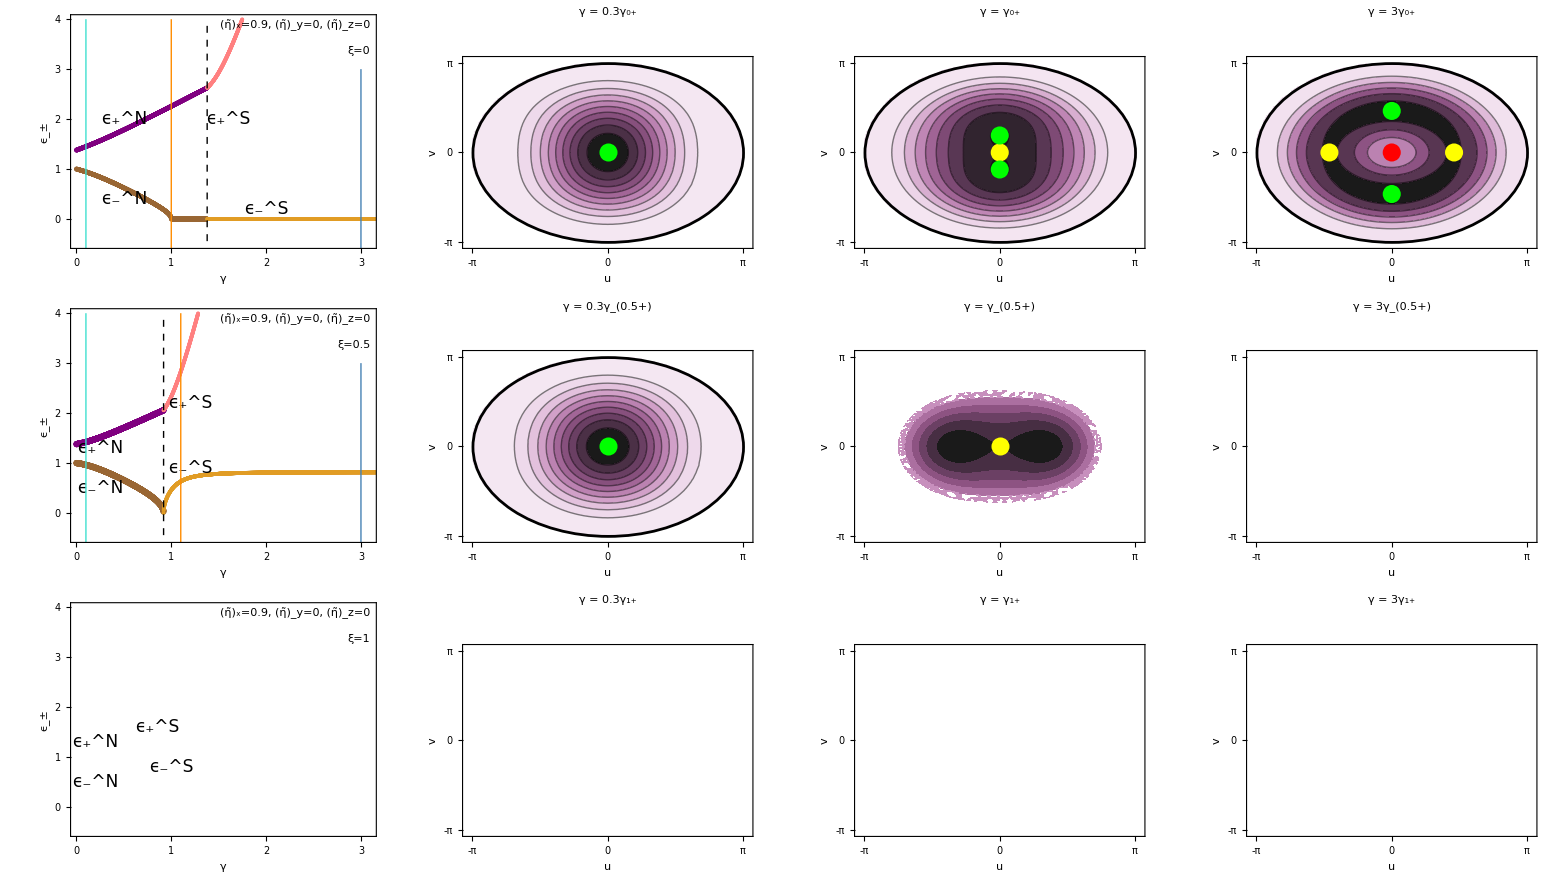

```mathematica
SetDirectory["/Users/rich/Documentos/07 Trimestre/Entropy Campo Medio/0_9 Interaction Value"];
exp=Grid[{{p[0.9,0,0,0,cT,cB,0.5,0.4,2,0.2,0.5,2,1.6,2,0.1,1,3],Surf1,Surf2,Surf3},
{p[0.9,0,0,0.5,cT,cB,0.25,0.5,1.2,0.9,0.25,1.3,1.2,2.2,0.1,1.1,3],Surf4,Surf5,Surf6},{p[0.9,0,0,1,cB,cB,0.2,0.5,1,0.8,0.2,1.3,0.85,1.6,0.1,1.1,3],Surf7,Surf8,Surf9}}]
Export["x-interaction.png",exp,ImageSize-> 2000,"CompressionLevel"->0,Background->White];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

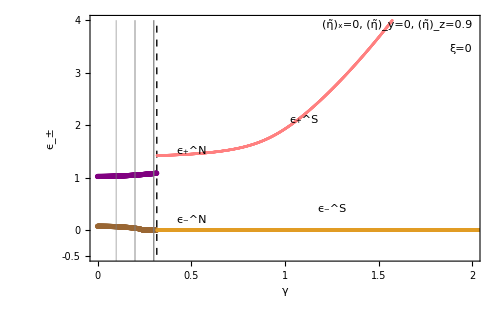
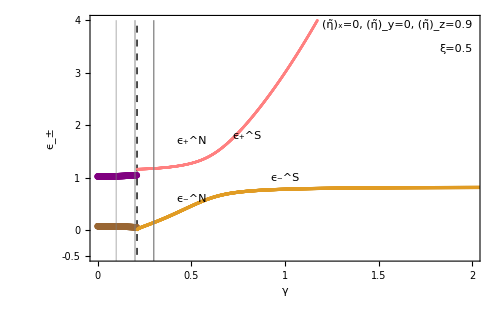
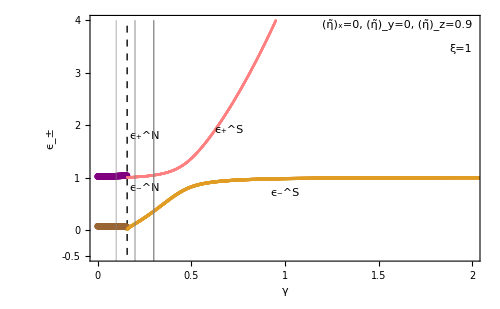
| -Graphics- | 
EC0 | EC0 | EC0
 | -Graphics- | 
EC0 | EC0 | EC0
 | -Graphics- | 
EC0 | EC0 | EC0

```mathematica
.
```